```mathematica
Remove["Global`*"]
e=Eo Cos[(ω z/c)-ω t]+2 Eo Cos[2(ω z/c)+2ω t];
b=Eo Cos[(ω z/c)-ω t]-2 Eo Cos[2(ω z/c)+2ω t];
u=(1/(8π))(e e + b b )//Expand
s=(c/(4π))Cross[{e,0,0},{0,b,0}][[3]]//Expand
j=(1/(4π))(-c D[b,z]-D[e,t])e//Expand;
D[u,t];
Dot[D[s,z],{0,0,1}] ;
Assuming[m∈Integers,Simplify[(ω/(2π))Integrate[u,{t,0,m π/ω},Assumptions->ω>0]]]
Assuming[n∈Integers,Simplify[(ω/(2π))Integrate[s,{t,0,n π/ω},Assumptions->ω>0]]]
```

(Eo^2 Cos[t ω-(z ω)/c]^2)/(4 π)+(Eo^2 Cos[2 t ω+(2 z ω)/c]^2)/π

(c Eo^2 Cos[t ω-(z ω)/c]^2)/(4 π)-(c Eo^2 Cos[2 t ω+(2 z ω)/c]^2)/π

(5 Eo^2 m)/(16 π)

-(3 c Eo^2 n)/(16 π)

```mathematica
Remove["Global`*"]
T=2π n/ωo
rect[t_]=Piecewise[{{1, -T/2≤t≤T/2}, {0, True}}];
e=Eo Cos[(ω z/c)-ω t]+2 Eo Cos[2(ω z/c)+2ω t]/.ω->ωo
ew[ω_]=FourierTransform[e,t,ω,FourierParameters->{-1,1}]
R[ω_]=(2 n)/ωo Sinc[(π n ω)/ωo]
eew[ω_]=Convolve[R[x],ew[x],x,ω]
```

(2 n π)/ωo

Eo Cos[t ωo-(z ωo)/c]+2 Eo Cos[2 t ωo+(2 z ωo)/c]

ⅇ^(-(2 ⅈ z ωo)/c) Eo DiracDelta[ω-2 ωo]+1/2 ⅇ^((ⅈ z ωo)/c) Eo DiracDelta[ω-ωo]+1/2 ⅇ^(-(ⅈ z ωo)/c) Eo DiracDelta[ω+ωo]+ⅇ^((2 ⅈ z ωo)/c) Eo DiracDelta[ω+2 ωo]

(2 n Sinc[(n π ω)/ωo])/ωo

1/ωo 2 n (ⅇ^(-(2 ⅈ z ωo)/c) Eo Sinc[(n π (ω-2 ωo))/ωo]+1/2 ⅇ^((ⅈ z ωo)/c) Eo Sinc[(n π (ω-ωo))/ωo]+1/2 ⅇ^(-(ⅈ z ωo)/c) Eo Sinc[(n π (ω+ωo))/ωo]+ⅇ^((2 ⅈ z ωo)/c) Eo Sinc[(n π (ω+2 ωo))/ωo])

1/π Abs[n (Sinc[1/2 n (-4 π+ω)]+1/2 Sinc[1/2 n (-2 π+ω)]+1/2 Sinc[1/2 n (2 π+ω)]+Sinc[1/2 n (4 π+ω)])]

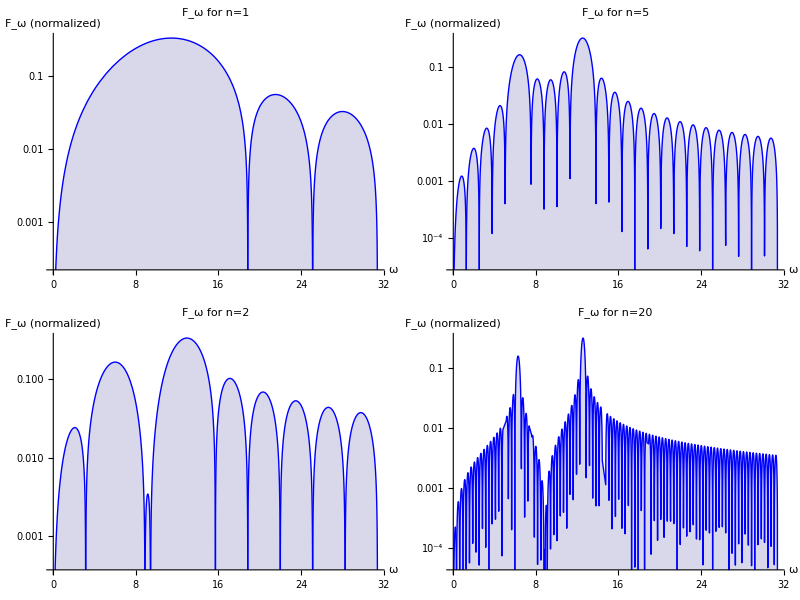

```mathematica
Abs[eew[ω]]/.ωo->2π/.Eo->1/.z->0
plot[m_]:=LogPlot[((1/T)Abs[eew[ω]])/.ωo->2π/.Eo->1/.z->0/.n->m,{ω,0,10π},ImageSize->Medium,PlotLabel->"F_ω for n="<>ToString[m]<>"",AxesLabel->{"ω","F_ω (normalized)"},Exclusions->None,Filling->Axis,PlotStyle->Blue]
Grid[{{plot[1],plot[5]},{plot[2],plot[20]}},Frame->All]
```

1/π(Sinc[1/2 n (-4 π+ω)]+1/2 Sinc[1/2 n (-2 π+ω)]+1/2 Sinc[1/2 n (2 π+ω)]+Sinc[1/2 n (4 π+ω)])

1/(2 π)(Sinc[n (π-ω/2)]+2 Sinc[1/2 n (-4 π+ω)]+Sinc[1/2 n (2 π+ω)]+2 Sinc[1/2 n (4 π+ω)])

Sinc[n (π-ω/2)]/(2 π)+Sinc[1/2 n (-4 π+ω)]/π+Sinc[1/2 n (2 π+ω)]/(2 π)+Sinc[1/2 n (4 π+ω)]/π

{(2 (8 π^2 ω+ω^3) Sin[ω/2])/(π (2 π-ω) (4 π-ω) (2 π+ω) (4 π+ω)),-(3 (8 π^2 ω-ω^3) Sin[ω])/(π (2 π-ω) (4 π-ω) (2 π+ω) (4 π+ω)),(2 (8 π^2 ω+ω^3) Sin[(3 ω)/2])/(3 π (2 π-ω) (4 π-ω) (2 π+ω) (4 π+ω)),-(3 (8 π^2 ω-ω^3) Sin[2 ω])/(2 π (2 π-ω) (4 π-ω) (2 π+ω) (4 π+ω)),(2 (8 π^2 ω+ω^3) Sin[(5 ω)/2])/(5 π (2 π-ω) (4 π-ω) (2 π+ω) (4 π+ω)),-((8 π^2 ω-ω^3) Sin[3 ω])/(π (2 π-ω) (4 π-ω) (2 π+ω) (4 π+ω)),(2 (8 π^2 ω+ω^3) Sin[(7 ω)/2])/(7 π (2 π-ω) (4 π-ω) (2 π+ω) (4 π+ω)),-(3 (8 π^2 ω-ω^3) Sin[4 ω])/(4 π (2 π-ω) (4 π-ω) (2 π+ω) (4 π+ω)),(2 (8 π^2 ω+ω^3) Sin[(9 ω)/2])/(9 π (2 π-ω) (4 π-ω) (2 π+ω) (4 π+ω)),-(3 (8 π^2 ω-ω^3) Sin[5 ω])/(5 π (2 π-ω) (4 π-ω) (2 π+ω) (4 π+ω)),(2 (8 π^2 ω+ω^3) Sin[(11 ω)/2])/(11 π (2 π-ω) (4 π-ω) (2 π+ω) (4 π+ω)),-((8 π^2 ω-ω^3) Sin[6 ω])/(2 π (2 π-ω) (4 π-ω) (2 π+ω) (4 π+ω)),(2 (8 π^2 ω+ω^3) Sin[(13 ω)/2])/(13 π (2 π-ω) (4 π-ω) (2 π+ω) (4 π+ω))}

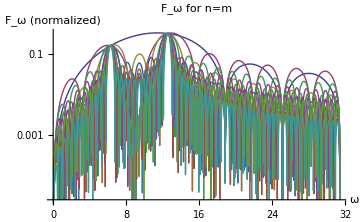

```mathematica
(1/T)eew[ω]/.ωo->2π/.Eo->1/.z->0
Assuming[n∈Integer,Simplify[%]]
TrigToExp[%]
Table[Series[%,{n,m,0}]//Normal,{m,1,13}]

Abs[%];

(*Limit[%,n->∞]*)
LogPlot[%,{ω,0,10π},ImageSize->Medium,PlotLabel->"F_ω for n="<>ToString[m]<>"",AxesLabel->{"ω","F_ω (normalized)"},Exclusions->None]
```

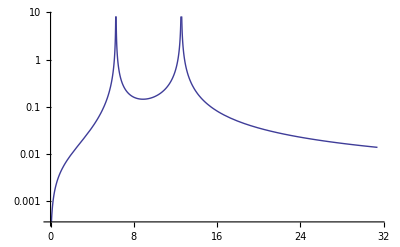

```mathematica
LogPlot[Abs[(8 π^2 ω+ω^3)/(π (2 π-ω) (4 π-ω) (2 π+ω) (4 π+ω))],{ω,0,10π}]
```

Piecewise[{{C ⅇ^(-(t γ)/2) Cos[t ωo], t≥0}, {0, True}}]

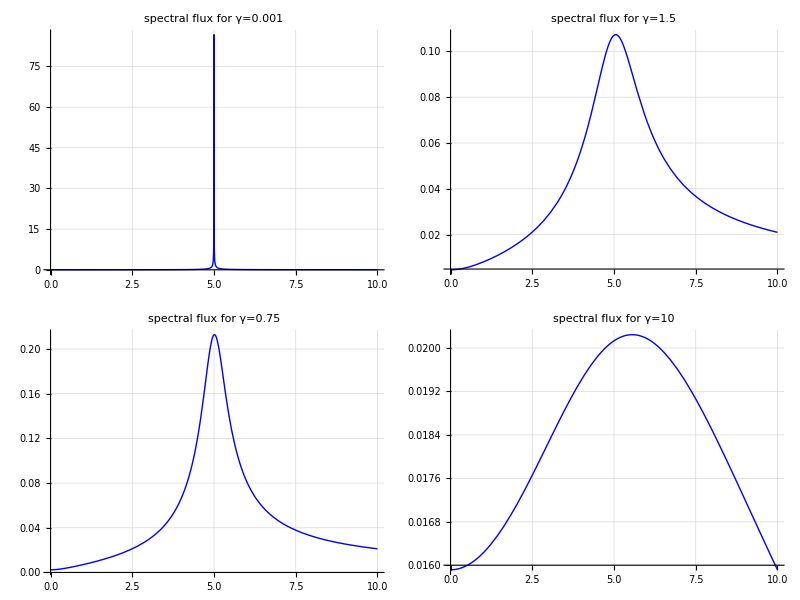

```mathematica
Remove["Global`*"]
e[t_]=Piecewise[{{C Exp[-γ t/2]Cos[ωo t], t≥0}, {0, True}}]
g=FourierTransform[e[t],t,ω,FourierParameters->{-1,1}];
plot2[n_]:=Plot[Abs[g]/.ωo->5/.C->1/.γ->n,{ω,0,10},GridLines->{5-n,5+n},PlotLabel->"spectral flux for γ="<>ToString[n]<>"",PlotStyle->Blue,Filling->Axes,PlotRange->All]
```

(2 C (γ-2 ⅈ ω))/(ωo (γ^2-4 ⅈ γ ω-4 ω^2+4 ωo^2))

(γ (γ-2 ⅈ ω) (γ-4 ⅈ ωo))/((γ-2 ⅈ ωo) (γ^2-4 ⅈ γ ω-4 ω^2+4 ωo^2))

{{ω→1/(2 (γ-2 ⅈ ωo))(2 γ ωo-√(-γ^4+8 ⅈ γ^3 ωo+20 γ^2 ωo^2-16 ⅈ γ ωo^3-16 ωo^4))},{ω→1/(2 (γ-2 ⅈ ωo))(2 γ ωo+√(-γ^4+8 ⅈ γ^3 ωo+20 γ^2 ωo^2-16 ⅈ γ ωo^3-16 ωo^4))}}

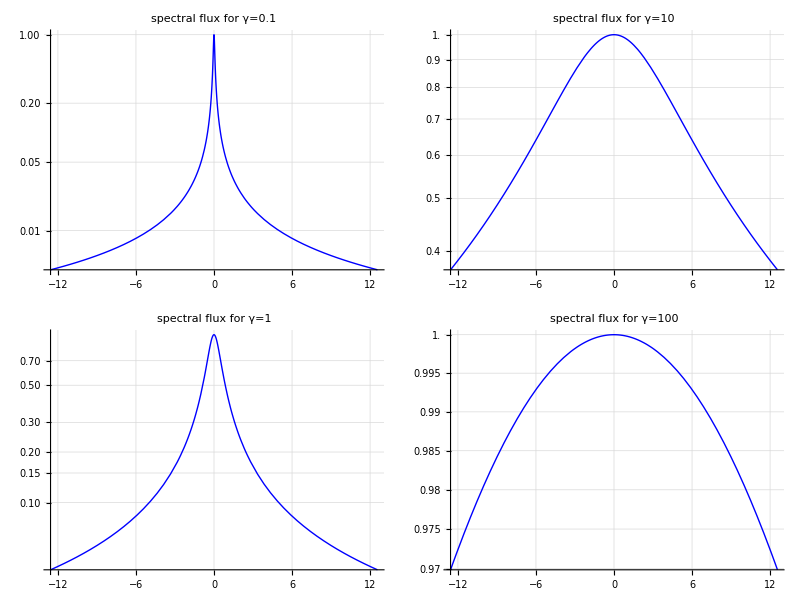

```mathematica
g2=(2π/ωo)g//TrigToExp//Simplify
g3=g2/Limit[g2,ω->ωo]//Simplify
Solve[Abs[g3]==1/2,ω][[{2,4}]]
plot2[n_,i_]:=LogPlot[(Abs[g3])/.ωo->0/.C->1/.γ->n,{ω,-4π n^i,4π n^i},GridLines->{5-n,5+n},PlotLabel->"spectral flux for γ="<>ToString[n]<>"  ",PlotStyle->Blue,Filling->Axes,PlotRange->{All,{0,1}},ImageSize->Medium]
Grid[{{plot2[.1,0],plot2[10,0]},{plot2[1,0],plot2[100,0]}},Frame->All]
```

```mathematica
Remove["Global`*"]
Manipulate[
stokesI=1;
Ex[t_]:=ℰ (Cos[β]Cos[χ]Cos[t]+Sin[β]Sin[χ]Sin[t]);
Ey[t_]:=ℰ (Cos[β]Sin[χ]Cos[t]-Sin[β]Cos[χ]Sin[t]);
χ:=(1/2)Piecewise[{{ArcTan[Abs[Sqrt[stokesI^2-V^2-Q^2]/Q]], Q≠0}, {π/2, Q==0}}];
β:=(1/2)ArcSin[Abs[V/stokesI]];
ℰ:=Sqrt[Sqrt[Q^2 + Sqrt[stokesI^2-V^2-Q^2]^2 + V^2]];
ParametricPlot[{{Ex[t], Ey[t]}},{t,0,2π},Axes->None,PlotRange->{{-1,1},{-1,1}},Frame->True,PlotStyle->Blue,ImageSize->Medium],{V,0,1},{Q,0,1}]
```